```mathematica
(* In this program we plot the mass of the u_b=u_λ solutions as a function of λ(b) for different values of d. For any given b, we first find λ(b) using bisection  method [with the tolerance specified by tolmin <- this not used yet]. We then solve the ODE for u_b for r between rmin and rmax. We use b values between b0 and bmax.
*)
```

## d = 4

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* define dimension d and bounds for the r-domain *)
d=4;
rmin=10^(-10);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
(* Equispaced grid points *)
(* b0 = 1;
bmax=100;
bvals = Range[b0,bmax]; *)
(* Grid points concentrated on smaller values of b *)
b0 = 0.36;
bmax = 10000;
logb0=Log[b0];
logbmax =Log[bmax];
logbvals = Subdivide[logb0,logbmax,100];
bvals=Exp[logbvals];
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+#1^3==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
(* The j-loop goes over the b-values defined in bvals. We append the λ(b) values to lamvals *)
For[j=1,j<=Length[bvals],j++,
If[Mod[j,10]==0,Print["Iteration number ",j],];
b=bvals[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
masstmp= NIntegrate[r^(d-1)*Evaluate[f1[r]^2/.solf],{r,rmin,6}];
masstmp=masstmp[[1]];
AppendTo[mass,masstmp];
AppendTo[lamvals,λ];
]
```

Iteration number10

Iteration number20

Iteration number30

Iteration number40

Iteration number50

Iteration number60

Iteration number70

Iteration number80

Iteration number90

Iteration number100

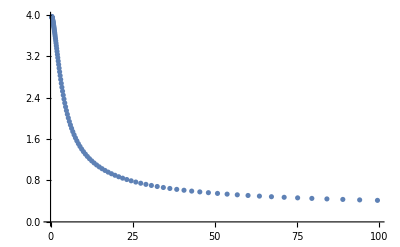

```mathematica
bversuslambdab = Transpose[{bvals,lamvals}];
ListPlot[bversuslambdab,PlotRange->All]
```

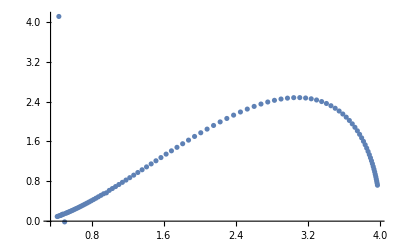

```mathematica
lambdaversusmass = Transpose[{lamvals,mass}];
ListPlot[lambdaversusmass,PlotRange->All]
```

## d = 5

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* define dimension d and bounds for the r-domain *)
d=5;
rmin=10^(-10);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
(* Equispaced grid points *)
(* b0 = 1;
bmax=100;
bvals = Range[b0,bmax]; *)
(* Grid points concentrated on smaller values of b *)
b0 = 0.36;
bmax = 10000;
logb0=Log[b0];
logbmax =Log[bmax];
logbvals = Subdivide[logb0,logbmax,100];
bvals=Exp[logbvals];
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+#1^3==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
(* The j-loop goes over the b-values defined in bvals. We append the λ(b) values to lamvals *)
For[j=1,j<=Length[bvals],j++,
If[Mod[j,10]==0,Print["Iteration number ",j],];
b=bvals[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
masstmp= NIntegrate[r^(d-1)*Evaluate[f1[r]^2/.solf],{r,rmin,6}];
masstmp=masstmp[[1]];
AppendTo[mass,masstmp];
AppendTo[lamvals,λ];
]
PrependTo[bvals,0];
PrependTo[lamvals,d];
PrependTo[mass,0];
```

Iteration number 10

Iteration number 20

Iteration number 30

Iteration number 40

Iteration number 50

Iteration number 60

Iteration number 70

Iteration number 80

Iteration number 90

Iteration number 100

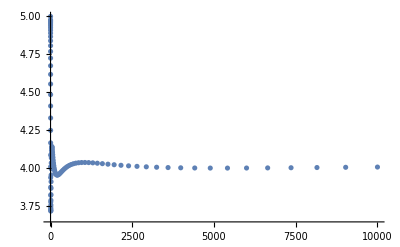

```mathematica
bversuslambdab = Transpose[{bvals,lamvals}];
ListPlot[bversuslambdab,PlotRange->All]
```

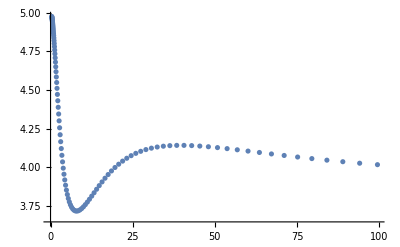

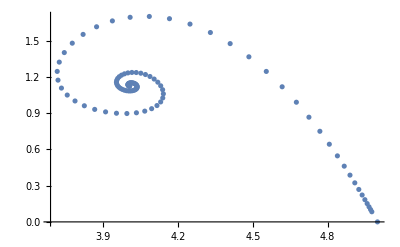

```mathematica
lambdaversusmass = Transpose[{lamvals,mass}];
MassPlot =ListPlot[lambdaversusmass,PlotRange->All]
```

```mathematica
(* Here, we find the limiting singular solution and calculate its mass. To find Subscript[λ, ∞], we use the bisection method *)
NLF={D[#2,r]+(d-3)/r #2-(d-3)/r^2 #1-r^2#1+#3 #1+1/r^2#1^3==0,#2==D[#1,r]}&;
boundF={#1[rmin]==Sqrt[d-3],#2[rmin]==0}&;
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Loop goes until either tolerance is satisfied, or maxiter is exceeded *)
tol=1;
For[i=1,tol>tolmin,i++,
solF=NDSolve[{NLF[F1[r],F2[r],λ],boundF[F1,F2]},{F1[r],F2[r]},{r,rmin,rmax}];
If[(F1[r]/.solF[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[F1[r]/.solF[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
Subscript[λ, ∞]=λ;
(* Note that when we compute the mass, we have r^(d-3) instead of r^(d-1). This is because F(r)=f(r)/r for the singular solution *)
masssing = NIntegrate[r^(d-3)*Evaluate[F1[r]^2/.solF],{r,rmin,6}];
```

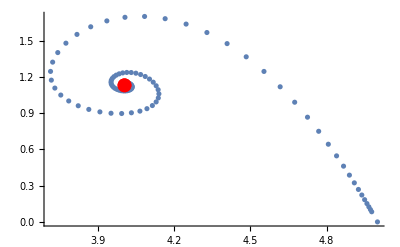

```mathematica
Show[MassPlot,ListPlot[{{Last[lamvals],masssing[[1]]}},PlotStyle->{PointSize[0.025],Red}],PlotRange->All]
```

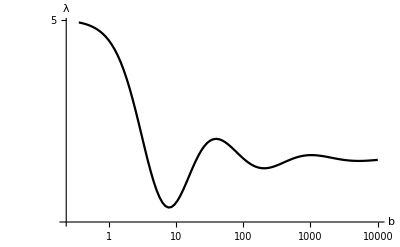

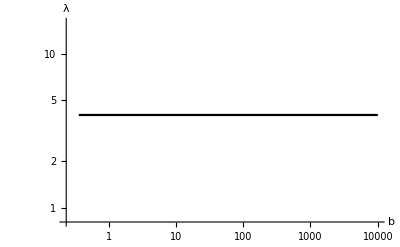

```mathematica
laminfvec=ConstantArray[Subscript[λ, ∞],Length[bvals]];
pltlam=ListLogLogPlot[Table[{bvals[[i]],lamvals[[i]]},{i,1,Length[bvals]}],Joined->True,PlotStyle->Black,AxesStyle->Directive[Black,Larger],AxesLabel->{"b","λ"}]
pltlaminf = ListLogLogPlot[Table[{bvals[[i]],laminfvec[[i]]},{i,1,Length[bvals]}],PlotStyle->Black,AxesStyle->Directive[Black,Larger],AxesLabel->{"b","λ"},Joined->True]
Show[pltlam,pltlaminf]
```

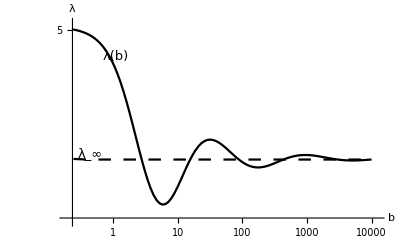

## d = 13

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* define dimension d and bounds for the r-domain *)
d=13;
rmin=10^(-10);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
(* Equispaced grid points *)
 (*b0 = 1/100;
bmax=1000;
bvals = Range[b0,bmax,10];*) 
(* Grid points concentrated on smaller values of b *)
b0 = 0.01;
bmax = 10000;
logb0=Log[b0];
logbmax =Log[bmax];
logbvals = Subdivide[logb0,logbmax,100];
bvals=Exp[logbvals];
(* Empty list to store the values λ(b) *)
lamvals = {};
(* Empty list to store the mass of u_b *)
mass = {};
(* Define the ODE and the ICs *)
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+#1^3==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;
(* The j-loop goes over the b-values defined in bvals. We append the λ(b) values to lamvals *)
For[j=1,j<=Length[bvals],j++,
If[Mod[j,10]==0,Print["Iteration number ",j],];
b=bvals[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
solf=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.solf[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.solf[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
masstmp= NIntegrate[r^(d-1)*Evaluate[f1[r]^2/.solf],{r,rmin,6}];
masstmp=masstmp[[1]];
AppendTo[mass,masstmp];
AppendTo[lamvals,λ];
]
PrependTo[bvals,0];
PrependTo[lamvals,d];
PrependTo[mass,0];
```

Iteration number 10

Iteration number 20

Iteration number 30

Iteration number 40

Iteration number 50

Iteration number 60

Iteration number 70

Iteration number 80

Iteration number 90

Iteration number 100

```mathematica
(* Here, we find the limiting singular solution and calculate its mass. To find Subscript[λ, ∞], we use the bisection method *)
NLF={D[#2,r]+(d-3)/r #2-(d-3)/r^2 #1-r^2#1+#3 #1+1/r^2#1^3==0,#2==D[#1,r]}&;
boundF={#1[rmin]==Sqrt[d-3],#2[rmin]==0}&;
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Loop goes until either tolerance is satisfied, or maxiter is exceeded *)
tol=1;
For[i=1,tol>tolmin,i++,
solF=NDSolve[{NLF[F1[r],F2[r],λ],boundF[F1,F2]},{F1[r],F2[r]},{r,rmin,rmax}];
If[(F1[r]/.solF[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[F1[r]/.solF[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
Subscript[λ, ∞]=λ;
(* Note that when we compute the mass, we have r^(d-3) instead of r^(d-1). This is because F(r)=f(r)/r for the singular solution *)
masssing = NIntegrate[r^(d-3)*Evaluate[F1[r]^2/.solF],{r,rmin,6}];
```

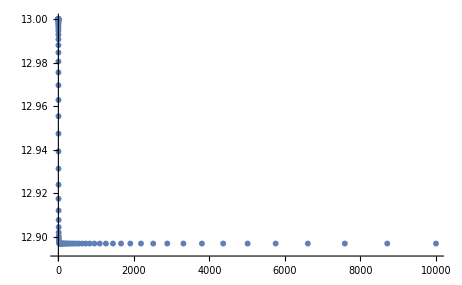

```mathematica
bversuslambdab = Transpose[{bvals,lamvals}];
ListPlot[bversuslambdab,PlotRange->All]
```

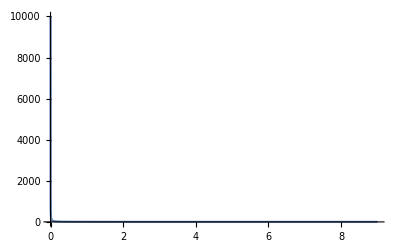

```mathematica
Plot[Evaluate[f1[r]/.solf],{r,rmin,rmax},PlotRange->All]
```

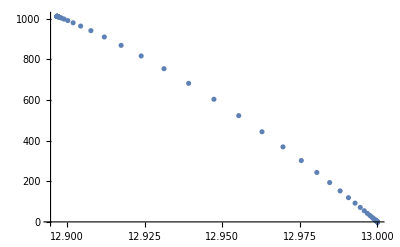

```mathematica
lambdaversusmass = Transpose[{lamvals,mass}];
MassPlot =ListPlot[lambdaversusmass,PlotRange->All]
```

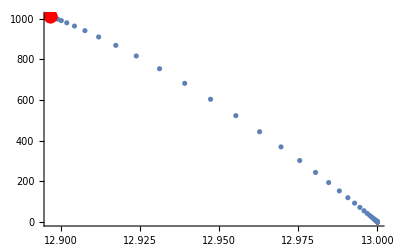

```mathematica
Show[MassPlot,ListPlot[{{Last[lamvals],masssing[[1]]}},PlotStyle->{PointSize[0.025],Red}],PlotRange->All]
```

```mathematica
(* Option with mass calculated inside NDSolve *)
(*
For[j=1,j<=Length[bvals],j++,
If[Mod[j,10]==0,Print["Iteration number ",j],];
b=bvals[[j]];
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Solve the b-IVP for the ground state in the r-variable, this is the starting point *)
sol=NDSolve[Join[NL2[f1[r],f2[r],λ],bound[f1,f2],{massfcn'[r]==r^(d-1)f1[r]^2,massfcn[rmin]==0}],{f1[r],f2[r],massfcn[r]},{r,rmin,rmax}];
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
sol=NDSolve[Join[NL2[f1[r],f2[r],λ],bound[f1,f2],{massfcn'[r]==r^(d-1)f1[r]^2,massfcn[rmin]==0}],{f1[r],f2[r],massfcn[r]},{r,rmin,rmax}];
If[(f1[r]/.sol[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.sol[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
(* Use the found value λ(b) to calculate mass of each ground state. We integrate u_b from rmin to rmax, using the weighted norm with the weight r^{d-1}. Here, we assume a cut-off at r=6 *)
(*masstmp= NIntegrate[r^(d-1)*Evaluate[f1[r]^2/.sol],{r,rmin,6}];
masstmp=masstmp[[1]];*)
masstmp =massfcn[r]/.sol[[1]]/.r->6;
AppendTo[mass,masstmp];
AppendTo[lamvals,λ];
]
*)
```

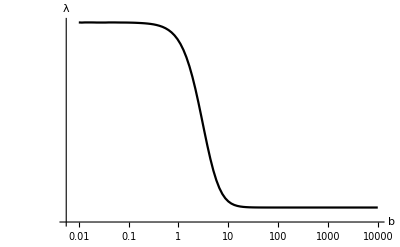

```mathematica
ListLogLogPlot[Table[{bvals[[i]],lamvals[[i]]},{i,1,Length[bvals]}],Joined->True,PlotStyle->Black,AxesStyle->Directive[Black,Larger],AxesLabel->{"b","λ"}]
```

```mathematica
MassPlot =ListPlot[lambdaversusmass,Joined->True,PlotStyle->Black,AxesStyle->Directive[Black,Larger]];
Show[MassPlot,ListPlot[{{Last[lamvals],masssing[[1]]}},PlotStyle->{PointSize[0.03],Red}],PlotRange->All,Frame->{{True,False},{True,False}},FrameStyle->Directive[Black,Larger],FrameLabel->{"λ","‖u_b‖_(L_r^2)^2"},RotateLabel->False]
```

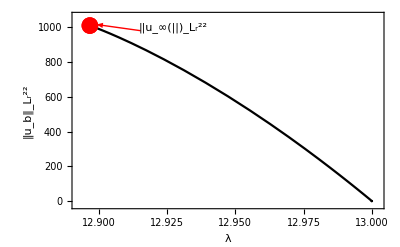

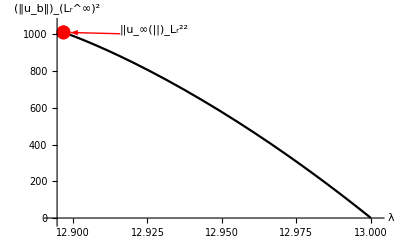

```mathematica
laminfvec=ConstantArray[Subscript[λ, ∞],Length[bvals]];
pltlam=ListLogLogPlot[Table[{bvals[[i]],lamvals[[i]]},{i,1,Length[bvals]}],Joined->True,PlotStyle->Black,AxesStyle->Directive[Black,Larger],AxesLabel->{"b","λ"}];
pltlaminf = ListLogLogPlot[Table[{bvals[[i]],laminfvec[[i]]},{i,1,Length[bvals]}],PlotStyle->Black,AxesStyle->Directive[Black,Larger],AxesLabel->{"b","λ"},Joined->True];
Show[pltlam,pltlaminf]
```